```mathematica
(1-(ab+d)/ad)*(1-(ab+d)/ad)^-1
```

1

```mathematica
(kV+g)/kg(kT-1/2 k^2 T^2+1/6 k^3 T^3)
```

((g+kV) (kT-(k^2 T^2)/2+(k^3 T^3)/6))/kg

```mathematica
Expand[(kV+g)/kg(kT-1/2 k^2 T^2+1/6 k^3 T^3)]
```

(g kT)/kg+(kT kV)/kg-(g k^2 T^2)/(2 kg)-(k^2 kV T^2)/(2 kg)+(g k^3 T^3)/(6 kg)+(k^3 kV T^3)/(6 kg)

```mathematica
T-(g kT)/kg-(kT kV)/kg
```

```mathematica
T(-kkV/kg-kg/kg)
T(-kV/g-1)
(-kV/g-1)^-1(-(g k^2 T^2)/(2 kg)-(k^2 kV T^2)/(2 kg)+(g k^3 T^3)/(6 kg)+(k^3 kV T^3)/(6 kg))
```

```mathematica
2/k-(2g)/(k(kV+g))
```

```mathematica
Simplify[2/k-(2g)/(k(kV+g))]
```

(2 kV)/(g k+k kV)

```mathematica
Simplify[-1+(kV+g)/g]
```

kV/g

```mathematica
Log[1-y]-Log[-y^2]+Log[y^2]
```

Log[1-y]-Log[-y^2]+Log[y^2]

```mathematica
Simplify[(1-y)/y^2]
```

(1-y)/y^2

```mathematica
Distribute[(kV+g)/kg(kT-1/2 k^2 T^2+1/6 k^3 T^3)]
```

(g kT)/kg+(kT kV)/kg-(g k^2 T^2)/(2 kg)-(k^2 kV T^2)/(2 kg)+(g k^3 T^3)/(6 kg)+(k^3 kV T^3)/(6 kg)

```mathematica
l=Log[E^2]
```

2

```mathematica
l
```

2

```mathematica
Clear[l]
```

```mathematica
l
```

l

```mathematica
Log[ⅇ^X]
```

Log[ⅇ^X]

```mathematica
D[Log[ⅇ^X], X]
```

1

```mathematica
∫_0^t 1/(1-f)*Log[f]ⅆf
```

ConditionalExpression[1/6 (π^2-3 Log[1-t] (Log[1-t]-2 Log[-t]+2 Log[t])-6 PolyLog[2,1/(1-t)]),Im[t]≠0||Re[t]≤1]

```mathematica
Log[E^(2θ)]
```

Log[ⅇ^(2 θ)]

```mathematica
Simplify[Log[E^(2θ)]]
```

Log[ⅇ^(2 θ)]

```mathematica
PowerExpand[Log[ⅇ^(2 θ)]]
```

2 θ

```mathematica
ExpandNumerator[(kV+g)/kg(kT-1/2 k^2 T^2+1/6 k^3 T^3)]
```

(g kT+kT kV-1/2 g k^2 T^2-1/2 k^2 kV T^2+1/6 g k^3 T^3+1/6 k^3 kV T^3)/kg

```mathematica
Collect[  (g kT+kT kV-1/2 g k^2 T^2-1/2 k^2 kV T^2+1/6 g k^3 T^3+1/6 k^3 kV T^3)/kg, T]
```

(g kT+kT kV)/kg+((-(g k^2)/2-(k^2 kV)/2) T^2)/kg+(((g k^3)/6+(k^3 kV)/6) T^3)/kg

```mathematica
Cancel[(g kT+kT kV)/kg+((-(g k^2)/2-(k^2 kV)/2) T^2)/kg+(((g k^3)/6+(k^3 kV)/6) T^3)/kg]
```

(g kT+kT kV)/kg-((g k^2+k^2 kV) T^2)/(2 kg)+((g k^3+k^3 kV) T^3)/(6 kg)

```mathematica
Factor[(g kT+kT kV)/kg]
```

(kT (g+kV))/kg

```mathematica
Cancel[(k T (g+kV))/(k g)]
```

((g+kV) T)/g

```mathematica
Simplify[((g+k V) T)/g ]
```

T+(k T V)/g

```mathematica
Collect[T+(k T V)/g,T]
```

T (1+(k V)/g)

```mathematica
ExpandNumerator[(kV+g)/kg(kT-1/2 k^2 T^2+1/6 k^3 T^3)]
```

(g kT+kT kV-1/2 g k^2 T^2-1/2 k^2 kV T^2+1/6 g k^3 T^3+1/6 k^3 kV T^3)/kg

```mathematica
Factor[(g kT+kT kV-1/2 g k^2 T^2-1/2 k^2 kV T^2+1/6 g k^3 T^3+1/6 k^3 kV T^3)/kg]
```

((g+kV) (6 kT-3 k^2 T^2+k^3 T^3))/(6 kg)

```mathematica
Cancel[(g kT+kT kV-1/2 g k^2 T^2-1/2 k^2 kV T^2+1/6 g k^3 T^3+1/6 k^3 kV T^3)/kg]
```

(6 g kT+6 kT kV-3 g k^2 T^2-3 k^2 kV T^2+g k^3 T^3+k^3 kV T^3)/(6 kg)

```mathematica
Cancel[1/(k g)(g  k T+k T k V-1/2 g  k^2  T^2-1/2 k^2  k V  T^2+1/6 g  k^3  T^3+1/6 k^3  k V  T^3)]
```

(6 g T-3 g k T^2+g k^2 T^3+6 k T V-3 k^2 T^2 V+k^3 T^3 V)/(6 g)

```mathematica
Factor[1/(k g)(g  k T+k T k V-1/2 g  k^2  T^2-1/2 k^2  k V  T^2+1/6 g  k^3  T^3+1/6 k^3  k V  T^3)]
```

(T (6-3 k T+k^2 T^2) (g+k V))/(6 g)

```mathematica
Simplify[1/(k g)(g  k T+k T k V-1/2 g  k^2  T^2-1/2 k^2  k V  T^2+1/6 g  k^3  T^3+1/6 k^3  k V  T^3)]
```

(T (6-3 k T+k^2 T^2) (g+k V))/(6 g)

```mathematica
(6 g)/T*((T (6-3 k T+k^2 T^2) (g+k V))/(6 g))
```

(6-3 k T+k^2 T^2) (g+k V)

```mathematica
Distribute[(6-3 k T+k^2 T^2) (g+k V)]
```

6 g-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V

```mathematica
6g==6 g-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V
```

6 g==6 g-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V

```mathematica
0==-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V
```

0==-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V

```mathematica
Solve[0==-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V, T]
```

{{T→(3 g+3 k V-√3 √(3 g^2-2 g k V-5 k^2 V^2))/(2 (g k+k^2 V))},{T→(3 g+3 k V+√3 √(3 g^2-2 g k V-5 k^2 V^2))/(2 (g k+k^2 V))}}

```mathematica
0==-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V
```

0==-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V

```mathematica
Collect[-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V,T]
```

6 k V+T (-3 g k-3 k^2 V)+T^2 (g k^2+k^3 V)

```mathematica
T (-3 g k-3 k^2 V)==-6 k V-T^2 (g k^2+k^3 V)
```

T (-3 g k-3 k^2 V)==-6 k V-T^2 (g k^2+k^3 V)

```mathematica
1/(-3 g k-3 k^2 V)*T (-3 g k-3 k^2 V)==(1/(-3 g k-3 k^2 V))*(-6 k V-T^2 (g k^2+k^3 V))
```

T==(-6 k V-T^2 (g k^2+k^3 V))/(-3 g k-3 k^2 V)

```mathematica
T==ExpandNumerator[(-6 k V-T^2 (g k^2+k^3 V))/(-3 g k-3 k^2 V)]
```

T==(-g k^2 T^2-6 k V-k^3 T^2 V)/(-3 g k-3 k^2 V)

```mathematica
T==Expand[(-6 k V-T^2 (g k^2+k^3 V))/(-3 g k-3 k^2 V)]
```

T==-(g k^2 T^2)/(-3 g k-3 k^2 V)-(6 k V)/(-3 g k-3 k^2 V)-(k^3 T^2 V)/(-3 g k-3 k^2 V)

```mathematica
T==Cancel[-(g k^2 T^2)/(-3 g k-3 k^2 V)]-Cancel[(6 k V)/(-3 g k-3 k^2 V)]-Cancel[(k^3 T^2 V)/(-3 g k-3 k^2 V)]
```

T==(g k T^2)/(3 (g+k V))+(2 V)/(g+k V)+(k^2 T^2 V)/(3 (g+k V))

```mathematica
T==Collect[(g k T^2)/(3 (g+k V))+(2 V)/(g+k V)+(k^2 T^2 V)/(3 (g+k V)),T]
```

T==(2 V)/(g+k V)+T^2 ((g k)/(3 (g+k V))+(k^2 V)/(3 (g+k V)))

```mathematica
T==(2 V)/(g+k V)+T^2 (Simplify[(g k)/(3 (g+k V))+(k^2 V)/(3 (g+k V))])
```

T==(k T^2)/3+(2 V)/(g+k V)

```mathematica
T==(k T^2)/3+((2 V)/((g+k V)/g))
```

T==(k T^2)/3+(2 g V)/(g+k V)

```mathematica
T==(k T^2)/3+(1/g*2 g V)/(1/g*(g+k V))
```

T==(k T^2)/3+(2 g V)/(g+k V)

```mathematica
Divide[g+k V,g]
```

(g+k V)/g

```mathematica
Simplify[(g+k V)/g]
```

1+(k V)/g

```mathematica
T==(k T^2)/3+Divide[2 V,g]/Simplify[Divide[g+k V,g]]
```

T==(k T^2)/3+(2 V)/(g (1+(k V)/g))

```mathematica
Cancel[  1/T*T  ]== Cancel[  1/T*((kT-1/2 k^2 T^2+1/6 k^3 T^3))]
```

1==(6 kT-3 k^2 T^2+k^3 T^3)/(6 T)

```mathematica
Cancel[  1/T*T  ]== Cancel[  1/T*((kV+g)/kg*(kT-1/2 k^2 T^2+1/6 k^3 T^3))]
```

1==((g+kV) (6 kT-3 k^2 T^2+k^3 T^3))/(6 kg T)

```mathematica
Cancel[  1/T*T  ]== Cancel[  1/T*((k V+g)/(k g)*(k T-1/2 k^2  T^2+1/6 k^3  T^3))]
```

1==((6-3 k T+k^2 T^2) (g+k V))/(6 g)

**Note this gets rid of common variables because of a space between each one.

```mathematica
Cancel[  1/T*T  ]== ExpandNumerator[Cancel[  1/T*((k V+g)/(k g)*(k T-1/2 k^2  T^2+1/6 k^3  T^3))]]
```

1==(6 g-3 g k T+g k^2 T^2+6 k V-3 k^2 T V+k^3 T^2 V)/(6 g)

```mathematica
Cancel[  1/T*T  ]== Collect[ExpandNumerator[Cancel[  1/T*((k V+g)/(k g)*(k T-1/2 k^2  T^2+1/6 k^3  T^3))]],T]
```

1==(6 g+6 k V)/(6 g)+(T (-3 g k-3 k^2 V))/(6 g)+(T^2 (g k^2+k^3 V))/(6 g)

```mathematica
1==Factor[6 g+6 k V]/(6 g)+Expand[T (-3 g k-3 k^2 V)]/(6 g)+Expand[T^2 (g k^2+k^3 V)]/(6 g)
```

1==(g+k V)/g+(-3 g k T-3 k^2 T V)/(6 g)+(g k^2 T^2+k^3 T^2 V)/(6 g)

```mathematica
Reduce[1==(g+k V)/g+(-3 g k T-3 k^2 T V)/(6 g)+(g k^2 T^2+k^3 T^2 V)/(6 g)]
```

(k==0&&g≠0)||(V==0&&T==0&&g≠0)||(T (-3+k T)≠0&&g==(-6 V+3 k T V-k^2 T^2 V)/(T (-3+k T))&&6 V-3 k T V+k^2 T^2 V≠0)||(V==0&&T≠0&&k==3/T&&g≠0)

```mathematica
-(g+k V)/g+1==-(g+k V)/g+(g+k V)/g+Collect[(-3 g k T-3 k^2 T V)/(6 g)+(g k^2 T^2+k^3 T^2 V)/(6 g),T]
```

1-(g+k V)/g==T (-k/2-(k^2 V)/(2 g))+T^2 (k^2/6+(k^3 V)/(6 g))

```mathematica
Simplify[1-(g+k V)/g]-T^2 (k^2/6+(k^3 V)/(6 g))==T (-k/2-(k^2 V)/(2 g))+T^2 (k^2/6+(k^3 V)/(6 g))-T^2 (k^2/6+(k^3 V)/(6 g))
```

-(k V)/g-T^2 (k^2/6+(k^3 V)/(6 g))==T (-k/2-(k^2 V)/(2 g))

```mathematica
Distribute[(-k/2-(k^2 V)/(2 g))^-1*(-(k V)/g-T^2 (k^2/6+(k^3 V)/(6 g)))]==T (-k/2-(k^2 V)/(2 g))*(-k/2-(k^2 V)/(2 g))^-1
```

-(k V)/(g (-k/2-(k^2 V)/(2 g)))-(T^2 (k^2/6+(k^3 V)/(6 g)))/(-k/2-(k^2 V)/(2 g))==T

```mathematica
Simplify[(-k/2-(k^2 V)/(2 g))^-1*(-(k V)/g-T^2 (k^2/6+(k^3 V)/(6 g)))]==T (-k/2-(k^2 V)/(2 g))*(-k/2-(k^2 V)/(2 g))^-1
```

(g k T^2+6 V+k^2 T^2 V)/(3 g+3 k V)==T

```mathematica
Expand[(g k T^2+6 V+k^2 T^2 V)/(3 g+3 k V)]==T
```

(g k T^2)/(3 g+3 k V)+(6 V)/(3 g+3 k V)+(k^2 T^2 V)/(3 g+3 k V)==T

```mathematica
Factor[(-k/2-(k^2 V)/(2 g))^-1*(-(k V)/g-T^2 (k^2/6+(k^3 V)/(6 g)))]==T (-k/2-(k^2 V)/(2 g))*(-k/2-(k^2 V)/(2 g))^-1
```

(g k T^2+6 V+k^2 T^2 V)/(3 (g+k V))==T

```mathematica
Cancel[(-k/2-(k^2 V)/(2 g))^-1*(-(k V)/g-T^2 (k^2/6+(k^3 V)/(6 g)))]==T (-k/2-(k^2 V)/(2 g))*(-k/2-(k^2 V)/(2 g))^-1
```

(g k T^2+6 V+k^2 T^2 V)/(3 (g+k V))==T

```mathematica
Collect[(g k T^2+6 V+k^2 T^2 V)/(3 (g+k V)),T]==T
```

(2 V)/(g+k V)+(T^2 (g k+k^2 V))/(3 (g+k V))==T

```mathematica
T==(2 V)/(g+k V)+Factor[(T^2 (g k+k^2 V))/(3 (g+k V))]
```

T==(k T^2)/3+(2 V)/(g+k V)

```mathematica
T==(k T^2)/3+Divide[2 V,g]/Simplify[g+k V]
```

T==(k T^2)/3+(2 V)/(g (g+k V))

```mathematica
T==(k T^2)/3+Divide[2 V,g]/Simplify[Divide[(g+k V),g]]
```

T==(k T^2)/3+(2 V)/(g (1+(k V)/g))

```mathematica
FunctionExpand[PolyLog[2,1-z]+PolyLog[2,z]]
```

π^2/6-Log[1-z] Log[z]

```mathematica
FunctionExpand[PolyLog[2,1-z]-PolyLog[2,1/z]]
```

PolyLog[2,1-z]-PolyLog[2,1/z]

```mathematica
FunctionExpand[-PolyLog[2,1/(1-z)]-PolyLog[2,1/z]]
```

-PolyLog[2,1/(1-z)]-PolyLog[2,1/z]

```mathematica
FunctionExpand[-PolyLog[2,1/(1-z)]+PolyLog[2,z]]
```

-PolyLog[2,1/(1-z)]+PolyLog[2,z]

```mathematica
FunctionExpand[PolyLog[3,1-z]+PolyLog[3,z]]
```

PolyLog[3,1-z]+PolyLog[3,z]

```mathematica
FunctionExpand[PolyLog[3,z]-PolyLog[3,1/z]]
```

1/(3 (1-z)^3)4 π^3 (-(1-z)^2/z^2)^(3/2) z^3 (1/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))-3/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^2+(1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^3)

```mathematica
Simplify[%]
```

1/6 Log[1/z] (-2 π^2-(3 π √(-(-1+z)^2/z^2) z Log[1/z])/(-1+z)+Log[1/z]^2)

```mathematica
Distribute[%]
```

-1/3 π^2 Log[1/z]-(π √(-(-1+z)^2/z^2) z Log[1/z]^2)/(2 (-1+z))+1/6 Log[1/z]^3

```mathematica
Simplify[-1/3 π^2 Log[1/z]-(π √(-(-1+z)^2/z^2) z Log[1/z]^2)/(2 (-1+z))]
```

1/6 π Log[1/z] (-2 π-(3 √(-(-1+z)^2/z^2) z Log[1/z])/(-1+z))

```mathematica
-1/3 π^2 PowerExpand[Log[z^-1]]-(π √(-(-1+z)^2/z^2)z PowerExpand[Log[1/z]]^2)/(2 (-1+z))+1/6 PowerExpand[Log[z^-1]]^3
```

1/3 π^2 Log[z]-(π √(-(-1+z)^2/z^2) z Log[z]^2)/(2 (-1+z))-Log[z]^3/6

```mathematica
PolyLog[3,z]==PolyLog[3,1/z]+1/3 π^2 Log[z]-(π Cancel[√(z^2*-(-1+z)^2/z^2) ] Log[z]^2)/(2 (-1+z))-Log[z]^3/6
```

PolyLog[3,z]==1/3 π^2 Log[z]-(π √(-(-1+z)^2) Log[z]^2)/(2 (-1+z))-Log[z]^3/6+PolyLog[3,1/z]

```mathematica
PolyLog[3,z]==1/3 π^2 Log[z]-(π *√-1*√((-1+z)^2) Log[z]^2)/(2 (-1+z))-Log[z]^3/6-PolyLog[3,1/z]
```

PolyLog[3,z]==1/3 π^2 Log[z]-(ⅈ π √((-1+z)^2) Log[z]^2)/(2 (-1+z))-Log[z]^3/6-PolyLog[3,1/z]

```mathematica
-(π √(-(-1+0)^2) Log[0]^2)/(2 (-1+0))
```

ⅈ ∞

```mathematica
Log[0]
```

-∞

```mathematica
-(π √(-(-1+1)^2) Log[1]^2)/(2 (-1+1))
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 π ComplexInfinity encountered.

Indeterminate

```mathematica
Simplify[1/(3 (1-z)^3)4 π^3 (-(1-z)^2/z^2)^(3/2) z^3 (1/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))-3/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^2+(1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^3), Assumptions-> 0<z<1]
```

1/6 (π+ⅈ Log[z]) (2 π+ⅈ Log[z]) Log[z]

```mathematica
Expand[1/6 (π+ⅈ Log[z]) (2 π+ⅈ Log[z]) Log[z]]
```

1/3 π^2 Log[z]+1/2 ⅈ π Log[z]^2-Log[z]^3/6

```mathematica
Simplify[-1/3 π^2 Log[1/z]-(π √(-(-1+z)^2/z^2) z Log[1/z]^2)/(2 (-1+z))+1/6 Log[1/z]^3, Assumptions -> 0<z<1]
```

-1/6 Log[z] (-2 π^2-3 ⅈ π Log[z]+Log[z]^2)

```mathematica
Expand[-1/6 Log[z] (-2 π^2-3 ⅈ π Log[z]+Log[z]^2)]
```

1/3 π^2 Log[z]+1/2 ⅈ π Log[z]^2-Log[z]^3/6

```mathematica
Log[-1]
```

ⅈ π

```mathematica
Expand[(A+B)^3]
```

A^3+3 A^2 B+3 A B^2+B^3

```mathematica
A=Log[-1]
B=Log[z]
Distribute[-1/6 Expand[(A+B)^3]]
```

ⅈ π

Log[z]

(ⅈ π^3)/6+1/2 π^2 Log[z]-1/2 ⅈ π Log[z]^2-Log[z]^3/6

```mathematica
(ⅈ π^3)/6+1/2 π^2 Log[z]-1/2 ⅈ π Log[z]^2-Log[z]^3/6-π^2/6 Log[-1]-π^2/6 Log[z]
```

1/3 π^2 Log[z]-1/2 ⅈ π Log[z]^2-Log[z]^3/6

```mathematica
1/3 π^2 Log[z]-1/2 ⅈ π Log[z]^2-Log[z]^3/6== -1/6 Log[-z]^3-π^2/6 Log[-z]
```

1/3 π^2 Log[z]-1/2 ⅈ π Log[z]^2-Log[z]^3/6==-1/6 π^2 Log[-z]-1/6 Log[-z]^3

```mathematica
PowerExpand[Log[-z]]
```

ⅈ π+Log[z]

```mathematica
PowerExpand[(Log[-z])]^3
```

(ⅈ π+Log[z])^3

```mathematica
Expand[(ⅈ π+Log[z])^3]
```

-ⅈ π^3-3 π^2 Log[z]+3 ⅈ π Log[z]^2+Log[z]^3

## Trilogarithm Identities

```mathematica
PolyLog[3,z]==PolyLog[3,1/z]+1/(3 (1-z)^3)4 π^3 (-(1-z)^2/z^2)^(3/2) z^3 (1/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))-3/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^2+(1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^3)==PolyLog[3,1/z]-1/3 π^2 Log[1/z]-(π √(-(-1+z)^2/z^2) z Log[1/z]^2)/(2 (-1+z))+1/6 Log[1/z]^3==PolyLog[3,1/z]+1/3 π^2 Log[z]-(π √(-(-1+z)^2/z^2) z Log[z]^2)/(2 (-1+z))-Log[z]^3/6==PolyLog[3,1/z]+1/3 π^2 Log[z]-(π √(-(-1+z)^2) Log[z]^2)/(2 (-1+z))-Log[z]^3/6==PolyLog[3,1/z]+1/6 (π+ⅈ Log[z]) (2 π+ⅈ Log[z]) Log[z]==PolyLog[3,1/z]+1/3 π^2 Log[z]+1/2 ⅈ π Log[z]^2-Log[z]^3/6==PolyLog[3,1/z]-1/6 π^2 Log[-z]-1/6 Log[-z]^3
```

PolyLog[3,z]==1/(3 (1-z)^3)4 π^3 (-(1-z)^2/z^2)^(3/2) z^3 (1/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))-3/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^2+(1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^3)+PolyLog[3,1/z]==-1/3 π^2 Log[1/z]-(π √(-(-1+z)^2/z^2) z Log[1/z]^2)/(2 (-1+z))+1/6 Log[1/z]^3+PolyLog[3,1/z]==1/3 π^2 Log[z]-(π √(-(-1+z)^2/z^2) z Log[z]^2)/(2 (-1+z))-Log[z]^3/6+PolyLog[3,1/z]==1/3 π^2 Log[z]-(π √(-(-1+z)^2) Log[z]^2)/(2 (-1+z))-Log[z]^3/6+PolyLog[3,1/z]==1/6 (π+ⅈ Log[z]) (2 π+ⅈ Log[z]) Log[z]+PolyLog[3,1/z]==1/3 π^2 Log[z]+1/2 ⅈ π Log[z]^2-Log[z]^3/6+PolyLog[3,1/z]==-1/6 π^2 Log[-z]-1/6 Log[-z]^3+PolyLog[3,1/z]

```mathematica
TraditionalForm[PolyLog[3,z]==1/(3 (1-z)^3)4 π^3 (-(1-z)^2/z^2)^(3/2) z^3 (1/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))-3/2 (1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^2+(1-(√(-(1-z)^2/z^2) z Log[1/z])/(2 π (1-z)))^3)+PolyLog[3,1/z]]
TraditionalForm[PolyLog[3,z]==-1/3 π^2 Log[1/z]-(π √(-(-1+z)^2/z^2) z Log[1/z]^2)/(2 (-1+z))+1/6 Log[1/z]^3+PolyLog[3,1/z]]
TraditionalForm[PolyLog[3,z]==1/3 π^2 Log[z]-(π √(-(-1+z)^2/z^2) z Log[z]^2)/(2 (-1+z))-Log[z]^3/6+PolyLog[3,1/z]]
TraditionalForm[PolyLog[3,z]==1/3 π^2 Log[z]-(π √(-(-1+z)^2) Log[z]^2)/(2 (-1+z))-Log[z]^3/6+PolyLog[3,1/z]]
TraditionalForm[PolyLog[3,z]==1/6 (π+ⅈ Log[z]) (2 π+ⅈ Log[z]) Log[z]+PolyLog[3,1/z]]
TraditionalForm[PolyLog[3,z]==1/3 π^2 Log[z]+1/2 ⅈ π Log[z]^2-Log[z]^3/6+PolyLog[3,1/z]]
TraditionalForm[PolyLog[3,z]==-1/6 π^2 Log[-z]-1/6 Log[-z]^3+PolyLog[3,1/z]]
```

3z==31/z+1/(3 (1-z)^3)4 π^3 (-(1-z)^2/z^2)^(3/2) z^3 ((1-(√(-(1-z)^2/z^2) z log(1/z))/(2 π (1-z)))^3-3/2 (1-(√(-(1-z)^2/z^2) z log(1/z))/(2 π (1-z)))^2+1/2 (1-(√(-(1-z)^2/z^2) z log(1/z))/(2 π (1-z))))

3z==31/z-(π √(-(z-1)^2/z^2) z log^2(1/z))/(2 (z-1))+1/6 log^3(1/z)-1/3 π^2 log(1/z)

3z==31/z-(π √(-(z-1)^2/z^2) z log^2(z))/(2 (z-1))-1/6 log^3(z)+1/3 π^2 log(z)

3z==31/z-1/6 log^3(z)-(π √(-(z-1)^2) log^2(z))/(2 (z-1))+1/3 π^2 log(z)

3z==31/z+1/6 (π+ⅈ log(z)) (2 π+ⅈ log(z)) log(z)

3z==31/z-1/6 log^3(z)+1/2 ⅈ π log^2(z)+1/3 π^2 log(z)

3z==31/z-1/6 log^3(-z)-1/6 π^2 log(-z)

```mathematica
FunctionExpand[PolyLog[2, 1/(1-z)]]
```

PolyLog[2,1/(1-z)]

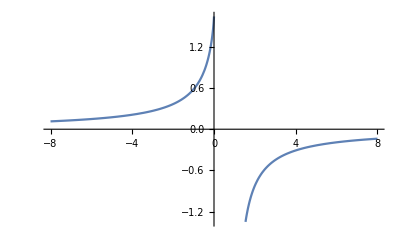

```mathematica
Plot[PolyLog[2,1/(1-z)],{z,-8,8}]
```

```mathematica
FunctionExpand[PolyLog[3,1/z]]
```

PolyLog[3,1/z]

```mathematica
Log[2^-1]^2==Log[2]^2
```

True

```mathematica
Log[1/2]Log[1/2]
```

Log[2]^2

```mathematica
Log[2^-1]Log[2^-1]
```

Log[2]^2

```mathematica
Log[1/2]Log[1/2]Log[1/2]
```

-Log[2]^3

```mathematica
Log[1/2]^3==-Log[2]^3
```

True

```mathematica
-Log[2]^2==Log[2]^2
```

False

```mathematica
Log[1/2]Log[2]
```

-Log[2]^2

```mathematica
Log[1/2]Log[2]Log[2]
```

-Log[2]^3

```mathematica
FunctionExpand[PolyLog[2,z]+PolyLog[2,1-z]]
```

π^2/6-Log[1-z] Log[z]

```mathematica
FunctionExpand[PolyLog[2,z]-PolyLog[2,1/(1-z)]]
```

-PolyLog[2,1/(1-z)]+PolyLog[2,z]

```mathematica
Distribute[PowerExpand[-Log[-z]Log[1-z]]]
```

-ⅈ π Log[1-z]-Log[1-z] Log[z]

```mathematica
PolyLog[2,1/(1-z)]==PolyLog[2,z]-1/2 Log[1-z]^2+ⅈ π Log[1-z]+Log[1-z] Log[z]+π^2/6
```

PolyLog[2,1/(1-z)]==π^2/6+ⅈ π Log[1-z]-1/2 Log[1-z]^2+Log[1-z] Log[z]+PolyLog[2,z]

```mathematica
1-z=2
```

Set::write: Tag Plus in 1-z is Protected.

2

```mathematica
PolyLog[2,1/2]==π^2/6+ⅈ π Log[2]-1/2 Log[2]^2+Log[2] Log[-1]+PolyLog[2,-1]
```

False

```mathematica
PolyLog[2,1/2]
```

π^2/12-Log[2]^2/2

```mathematica
PolyLog[2,-1]
```

-π^2/12

```mathematica
PolyLog[2,1/2]-PolyLog[2,-1]
```

π^2/6-Log[2]^2/2

```mathematica
Clear[x]
```

```mathematica
H==π^2/6+ⅈ π Log[1-x]-1/2 Log[1-x]^2-PolyLog[2,1/(1-x)]
-PolyLog[2,1/(1-x)]==-PolyLog[2,x]+1/2 Log[1-x]^2-ⅈ π Log[1-x]-Log[1-x] Log[x]-π^2/6
```

H==π^2/6+ⅈ π Log[1-x]-1/2 Log[1-x]^2-PolyLog[2,1/(1-x)]

-PolyLog[2,1/(1-x)]==-π^2/6-ⅈ π Log[1-x]+1/2 Log[1-x]^2-Log[1-x] Log[x]-PolyLog[2,x]

```mathematica
H==π^2/6+ⅈ π Log[1-x]-1/2 Log[1-x]^2-π^2/6-ⅈ π Log[1-x]+1/2 Log[1-x]^2-Log[1-x] Log[x]-PolyLog[2,x]
```

H==-Log[1-x] Log[x]-PolyLog[2,x]

```mathematica
-PolyLog[2,1/2]-Log[1/2]Log[1/2]+π^2/6
```

π^2/12-Log[2]^2/2

```mathematica
2PolyLog[2,1/2]==-Log[1/2]Log[1/2]+π^2/6
```

True

```mathematica
PowerExpand[Log[1/z]^2]
```

Log[z]^2

```mathematica
PowerExpand[Log[z]^2]
```

Log[z]^2

```mathematica
PowerExpand[Log[1/z]^2]== PowerExpand[Log[z]^2]
```

True

```mathematica
PowerExpand[Log[1/z]^3]== PowerExpand[Log[z]^3]
```

-Log[z]^3==Log[z]^3

```mathematica
PowerExpand[-Log[1/z]^2]== PowerExpand[Log[z]^2]
```

-Log[z]^2==Log[z]^2

```mathematica
PowerExpand[(Log[z^-1])^2]== PowerExpand[Log[z]^2]
```

True

```mathematica
PowerExpand[Log[a]/Log[b]]
```

Log[a]/Log[b]

```mathematica
FullSimplify[Log[a/b]/Log[b/c]]
```

Log[a/b]/Log[b/c]

Log[y] (PolyLog[2,y]-2 PolyLog[3,y])

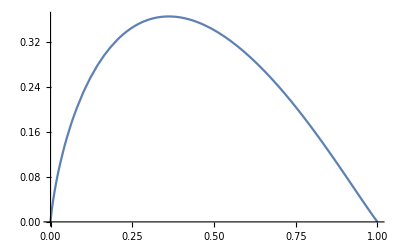

```mathematica
r4=Log[y] (PolyLog[2,y]-2 PolyLog[3,y])
Plot[r4,{y,0,1}]
```

```mathematica
D[m, m]*f
```

f

```mathematica
d[x Log[x^2],x]/.ProductRule
```

x d[Log[x^2],x]+d[x,x] Log[x^2]

```mathematica
x D[Log[x^2],x]+D[x,x] Log[x^2]
```

2+Log[x^2]

```mathematica
D[Log[x^2],x]
```

2/x

```mathematica
d[e m^(ϵ/2)(1+ e^2/(12 π^2 ϵ)), m]/.ProductRule
```

```mathematica
m^(ϵ/2) (1+e^2/(12 π^2 ϵ)) d[e,m]+e d[m^(ϵ/2) (1+e^2/(12 π^2 ϵ)),m], wrong
```

```mathematica
Distribute[e m^(ϵ/2)(1+ e^2/(12 π^2 ϵ))]
```

e m^(ϵ/2)+(e^3 m^(ϵ/2))/(12 π^2 ϵ)

```mathematica
d[e m^(ϵ/2),m]+1/(12 π^2 ϵ)d[e^3 m^(ϵ/2),m] /.ProductRule
```

m^(ϵ/2) d[e,m]+e d[m^(ϵ/2),m]+(m^(ϵ/2) d[e^3,m]+e^3 d[m^(ϵ/2),m])/(12 π^2 ϵ)

```mathematica
m^(ϵ/2) d[e,m]+e d[m^(ϵ/2),m]+FactorTerms[(m^(ϵ/2) d[e^3,m]+e^3 d[m^(ϵ/2),m])/(12*π^2*ϵ)]
```

m^(ϵ/2) d[e,m]+e d[m^(ϵ/2),m]+1/12 ((m^(ϵ/2) d[e^3,m])/(π^2 ϵ)+(e^3 d[m^(ϵ/2),m])/(π^2 ϵ))

```mathematica
WalkD[m^(ϵ/2),m]
```

d[m^(ϵ/2),m]

PowerRule

=    1/2 m^(-1+ϵ/2) ϵ

1/2 m^(-1+ϵ/2) ϵ

```mathematica
d[e^3,m]/.ChainRule
```

3 e^2 d[e,m]

```mathematica
m^(ϵ/2) d[e,m]+e  (1/2 m^(-1+ϵ/2) ϵ)+ExpandAll[(m^(ϵ/2) (3 e^2 d[e,m])+e^3 (1/2 m^(-1+ϵ/2) ϵ))/(12 π^2 ϵ)]
```

(e^3 m^(-1+ϵ/2))/(24 π^2)+1/2 e m^(-1+ϵ/2) ϵ+m^(ϵ/2) d[e,m]+(e^2 m^(ϵ/2) d[e,m])/(4 π^2 ϵ)

```mathematica
Collect[(e^3 m^(-1+ϵ/2))/(24 π^2)+1/2 e m^(-1+ϵ/2) ϵ+m^(ϵ/2) d[e,m]+(e^2 m^(ϵ/2) d[e,m])/(4 π^2 ϵ), d[e,m]]
```

```mathematica
Collect[(e^3 m^(-1+ϵ/2))/(24 π^2)+1/2 e m^(-1+ϵ/2) ϵ,m^(ϵ/2)]+Collect[(m^(ϵ/2)+(e^2 m^(ϵ/2))/(4 π^2 ϵ)) d[e,m],m^(ϵ/2)]
```

m^(ϵ/2) (e^3/(24 m π^2)+(e ϵ)/(2 m))+m^(ϵ/2) (1+e^2/(4 π^2 ϵ)) d[e,m]

```mathematica
m^(ϵ/2) (e^3/(24 m π^2)+(e ϵ)/(2 m))+m^(ϵ/2) (1+e^2/(4 π^2 ϵ)) d[e,m]==0
```

m^(ϵ/2) (e^3/(24 m π^2)+(e ϵ)/(2 m))+m^(ϵ/2) (1+e^2/(4 π^2 ϵ)) d[e,m]==0

```mathematica
Solve[m^(ϵ/2) (e^3/(24 m π^2)+(e ϵ)/(2 m))+m^(ϵ/2) (1+e^2/(4 π^2 ϵ)) d[e,m]==0, d[e,m]]
```

{{d[e,m]→-(ϵ (e^3+12 e π^2 ϵ))/(6 m (e^2+4 π^2 ϵ))}}

```mathematica
Divide[m^(ϵ/2) (e^3/(24 m π^2)+(e ϵ)/(2 m)),m^(ϵ/2)]+Divide[m^(ϵ/2) (1+e^2/(4 π^2 ϵ)) d[e,m],m^(ϵ/2)]==0
```

```mathematica
-e^3/(24 m π^2)-(e ϵ)/(2 m)+e^3/(24 m π^2)+(e ϵ)/(2 m)+(1+e^2/(4 π^2 ϵ)) d[e,m]==0-e^3/(24 m π^2)-(e ϵ)/(2 m)
```

```mathematica
(1+e^2/(4 π^2 ϵ))^-1(1+e^2/(4 π^2 ϵ)) d[e,m]==(-e^3/(24 m π^2)-(e ϵ)/(2 m))*Series[(1+e^2/(4 π^2 ϵ))^-1,{e^2/(4 π^2 ϵ),0,3}]
```

d[e,m]==(-e^3/(24 m π^2)-(e ϵ)/(2 m)) Series[1/(1+e^2/(4 π^2 ϵ)),{e^2/(4 π^2 ϵ),0,3}]

```mathematica
ExpandAll[(1+e^2/(4 π^2 ϵ))^-1]
```

1/(1+e^2/(4 π^2 ϵ))

```mathematica
x=.
```

```mathematica
Series[(1+x)^-1,{x,0,3}]
```

```mathematica
1-x+x^2-x^3+O[x]^4
```

```mathematica
x=e^2/(4 π^2 ϵ)
```

e^2/(4 π^2 ϵ)

```mathematica
1-x
```

1-e^2/(4 π^2 ϵ)

```mathematica
Distribute[-e ϵ/2*(1+e^2/(12 π^2 ϵ))]*(1-e^2/(4 π^2 ϵ))
```

(1-e^2/(4 π^2 ϵ)) (-e^3/(24 π^2)-(e ϵ)/2)

```mathematica
Expand[-e ϵ/2*(1+e^2/(12 π^2 ϵ))*(1-e^2/(4 π^2 ϵ))]
```

e^3/(12 π^2)+e^5/(96 π^4 ϵ)-(e ϵ)/2

```mathematica
d[ e^2,m] /.ChainRule
```

2 e d[e,m]

```mathematica
Series[(1+t)^-1,{t,0,4}]
```

1-t+t^2-t^3+t^4+O[t]^5

Identity:  3z = -3z/(z-1)-31-z+1/6 log^3(1-z)-1/2 log(z)log^2(1-z)+1/6 π^2 log(1-z)+ζ(3)  
                     -3z = 3z/(z-1)+31-z-1/6 log^3(1-z)+1/2 log(z)log^2(1-z)-1/6 π^2 log(1-z)-ζ(3)    
                    -23z = 23z/(z-1)+231-z-1/3 log^3(1-z)+log(z)log^2(1-z)-1/3 π^2 log(1-z)-2ζ(3)
 
                    2z =-21-z-log(z)log(1-z)+π^2/6
                   2-z =-21+z-log(-z)log(1+z)+π^2/6
                    2-z =-21+z-ⅈπ log(1+z)-log(z)log(1+z)+π^2/6

                    2z =21/(1-z)+1/2 log^2(1-z)-log(-z)log(1-z)-π^2/6
                    2z =21/(1-z)+1/2 log^2(1-z)-ⅈπ log(1-z)-log(z)log(1-z)-π^2/6
                    2-z =21/(1+z)+1/2 log^2(1+z)-log(z)log(1+z)-π^2/6

```mathematica
-Distribute[PowerExpand[Log[-z]Log[1-z]]]
```

-ⅈ π Log[1-z]-Log[1-z] Log[z]

```mathematica
PolyLog[2,z]+PolyLog[2,1-z]==1/2 Log[1-z]^2-ⅈ π Log[1-z]-Log[1-z] Log[z]-π^2/6==-Log[1-z]Log[z]+π^2/6
```

PolyLog[2,1-z]+PolyLog[2,z]==-π^2/6-ⅈ π Log[1-z]+1/2 Log[1-z]^2-Log[1-z] Log[z]==π^2/6-Log[1-z] Log[z]

```mathematica
PolyLog[2,-z]+PolyLog[2,1+z]==-ⅈ π Log[1+z]-Log[1+z] Log[z]+π^2/6==1/2 Log[1+z]^2-Log[1+z]Log[z]-π^2/6
```

PolyLog[2,-z]+PolyLog[2,1+z]==π^2/6-ⅈ π Log[1+z]-Log[z] Log[1+z]==-π^2/6-Log[z] Log[1+z]+1/2 Log[1+z]^2

```mathematica
PolyLog[2,1/2]
PolyLog[3,1/2]
FunctionExpand[PolyLog[4,1/2]]
PolyLog[5,1/2]
```

π^2/12-Log[2]^2/2

1/24 (-2 π^2 Log[2]+4 Log[2]^3+21 Zeta[3])

PolyLog[4,1/2]

PolyLog[5,1/2]

Log[1-a] Log[2/(1+a)]+PolyLog[2,-1/2]-PolyLog[2,(1-a)/2]

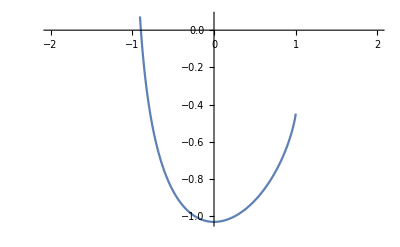

```mathematica
H10b=PolyLog[2,-1/2]+Log[1-a] Log[2/(1+a)]-PolyLog[2,(1-a)/2]
Plot[H10b, {a, -2,2}]
```

```mathematica
PolyLog[2,-1/2]
```

PolyLog[2,-1/2]